```mathematica
ClearAll["Global`*"]
tval=2;
L = 10;
v0 =0.1;
f0 = 0.6;
θ = π/4;
A = 0.4;
Al = A*0.6;
eqn = D[ h[x,t],t] ==-v0*Exp[(Tan[θ]-D[h[x,t],x])/Al-f0/A]*(D[h[x,t],x]-h[x,t]/Al*D[h[x,t],x,x])
BC = {h[-L,t]==1,h[L,t]==0};
(*ICfun = 0.5-1/π*ArcTan[x/0.05]*)
ICfun = 0.5*Erfc[(x+L/2)/0.2];
(*ICfun = Piecewise[{{-0.2*x,x<0}},0];*)
IC = h[x,0] == ICfun;
sol = NDSolve[{eqn,IC,BC},h,{x,-L,L},{t,0,tval},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->100,"MaxPoints"->5000}}];
```

h^(0,1)[x,t]==-0.1 ⅇ^(-1.5+4.16667 (1-h^(1,0)[x,t])) (h^(1,0)[x,t]-4.16667 h[x,t] h^(2,0)[x,t])

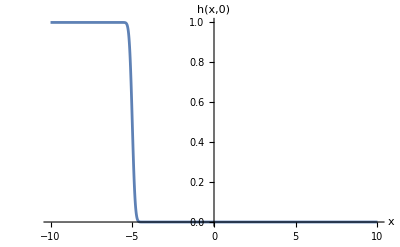

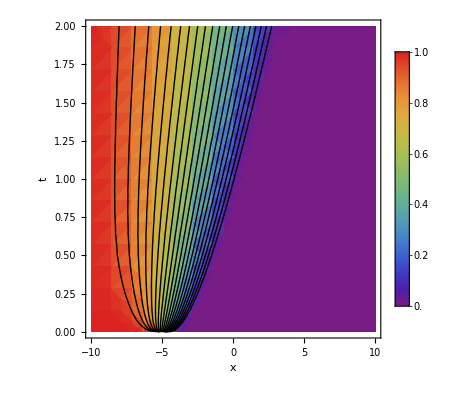

```mathematica
Plot[ICfun,{x,-L,L},AxesLabel->{"x","h(x,0)"},PlotRange->Full]
Show[
DensityPlot[
Evaluate[h[x,t]/. sol],{x,-L,L},{t,0,tval},ColorFunction->"Rainbow",PlotLegends->BarLegend[{"Rainbow",{0,1}}], FrameLabel->{"x","t"}
],
ContourPlot[
Evaluate[h[x,t]/. sol],{x,-L,L},{t,0,tval},
Contours->20,(*Number of contour lines*)
ContourStyle->Black,(*Make contours stand out*)
ContourShading->None (*Remove fill to show DensityPlot underneath*)
],
ScalingFunctions->{"Linear","Linear"}
]
```

```mathematica
tValues={0,0.01,0.05,0.1,0.2,0.4,0.6,0.7,0.8,0.9,1.0}*tval; (*Choose different t values*)
(*tValues={1,2,3,4,5,6};*)
Plot[Evaluate@Table[h[x,t]/. sol,{t,tValues}],{x,-L,L},PlotStyle->Table[Directive[Thick,ColorData[10][i]],{i,Length[tValues]}],PlotLegends->Placed[LineLegend[tValues,LabelStyle->{10}],{1.0,0.6}],Frame->True,FrameLabel->{"x","h(x,t)"},LabelStyle->{14,Bold},Axes->False,ImageSize->Large]
```

-Graphics-